```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 29 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[zReplace]
zReplace =  { 
z[t] ->  x[t]^2+y[t]^2 - x[t]  y[t]  
}
```

{z[t]→x[t]^2-x[t] y[t]+y[t]^2}

```mathematica
D[zReplace, t] 
D[zReplace, t]  // Simplify  // pdConv
Collect[ D[zReplace, t]  , {x'[t] , y'[t] } ] // pdConv
```

{z'[t]→2 x[t] x'[t]-y[t] x'[t]-x[t] y'[t]+2 y[t] y'[t]}

{(∂z(t))/(∂t)→x(t) (2 (∂x(t))/(∂t)-(∂y(t))/(∂t))-y(t) ((∂x(t))/(∂t)-2 (∂y(t))/(∂t))}

{(∂z(t))/(∂t)→(2 x(t)-y(t)) (∂x(t))/(∂t)+(2 y(t)-x(t)) (∂y(t))/(∂t)}

```mathematica
D[D[zReplace, t], t]
```

{z''[t]→2 x'[t]^2-2 x'[t] y'[t]+2 y'[t]^2+2 x[t] x''[t]-y[t] x''[t]-x[t] y''[t]+2 y[t] y''[t]}

```mathematica
Plot3D[ x^2+y^2 - x y , { x , -3, 3 } , { y, -3 , 3 }  , AxesLabel-> { x , y, z } ]
```

-Graphics3D-

```mathematica
Plot3D[ z[t] /. zReplace , { x[t] , - 3, 3 } , { y[t] , -3 , 3 } , AxesLabel-> { x[t] , y[t] , z[t] }  ]
```

-Graphics3D-

```mathematica
Clear[r]
r = { x[t] , y[t] , z[t] }
```

{x[t],y[t],z[t]}

```mathematica
D[r, t]
```

{x'[t],y'[t],z'[t]}

```mathematica
D[r, t] . D[r, t] // Expand  // Simplify  // pdConv
```

((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2+((∂z(t))/(∂t))^2

```mathematica
D[r, t] . D[r, t] /. D[zReplace, t] 
D[r, t] . D[r, t] /. D[zReplace, t]  // Simplify 
D[r, t] . D[r, t] /. D[zReplace, t]  // pdConv
D[r, t] . D[r, t] /. D[zReplace, t]   // Simplify // pdConv
```

x'[t]^2+y'[t]^2+(2 x[t] x'[t]-y[t] x'[t]-x[t] y'[t]+2 y[t] y'[t])^2

x'[t]^2+y'[t]^2+(y[t] (x'[t]-2 y'[t])+x[t] (-2 x'[t]+y'[t]))^2

(-x(t) (∂y(t))/(∂t)-y(t) (∂x(t))/(∂t)+2 x(t) (∂x(t))/(∂t)+2 y(t) (∂y(t))/(∂t))^2+((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2

(x(t) ((∂y(t))/(∂t)-2 (∂x(t))/(∂t))+y(t) ((∂x(t))/(∂t)-2 (∂y(t))/(∂t)))^2+((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2

```mathematica
Clear[T]
T = 1/2 m ( D[r, t] . D[r, t] /. D[zReplace, t] )  ;
T // pdConv
```

1/2 m ((-x(t) (∂y(t))/(∂t)-y(t) (∂x(t))/(∂t)+2 x(t) (∂x(t))/(∂t)+2 y(t) (∂y(t))/(∂t))^2+((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2)

```mathematica
Clear[V]
V = 
m g z[t] /. zReplace
```

g m (x[t]^2-x[t] y[t]+y[t]^2)

```mathematica
Clear[ℒ]
ℒ = T - V ; 
ℒ // pdConv
```

1/2 m ((-x(t) (∂y(t))/(∂t)-y(t) (∂x(t))/(∂t)+2 x(t) (∂x(t))/(∂t)+2 y(t) (∂y(t))/(∂t))^2+((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2)-g m (-x(t) y(t)+(x(t))^2+(y(t))^2)

```mathematica
Clear[q]
q = { x[t] , y[t] }
```

{x[t],y[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ]  // Expand // FullSimplify 
D[ D[ ℒ , D[q[[2]], t] ], t ]  - D[ ℒ , q[[2]] ]  // Expand // FullSimplify
```

m (x''[t]+(2 x[t]-y[t]) (g+2 (x'[t]^2-x'[t] y'[t]+y'[t]^2)+(2 x[t]-y[t]) x''[t]-(x[t]-2 y[t]) y''[t]))

-m (x[t]-2 y[t]) (g+2 (x'[t]^2-x'[t] y'[t]+y'[t]^2)+(2 x[t]-y[t]) x''[t])+m (1+(x[t]-2 y[t])^2) y''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] // Expand // FullSimplify ;
eqs // TableForm
```

m (x''[t]+(2 x[t]-y[t]) (g+2 (x'[t]^2-x'[t] y'[t]+y'[t]^2)+(2 x[t]-y[t]) x''[t]-(x[t]-2 y[t]) y''[t]))==0
m (x[t]-2 y[t]) (g+2 (x'[t]^2-x'[t] y'[t]+y'[t]^2)+(2 x[t]-y[t]) x''[t])==m (1+(x[t]-2 y[t])^2) y''[t]

```mathematica
Clear[parameters]
parameters = {
m-> 2 , 
g-> 9.8 
} ;
parameters // TableForm
```

m→2
g→9.8

```mathematica
eqs /. parameters // Expand // TableForm
```

39.2 x[t]-19.6 y[t]+8 x[t] x'[t]^2-4 y[t] x'[t]^2-8 x[t] x'[t] y'[t]+4 y[t] x'[t] y'[t]+8 x[t] y'[t]^2-4 y[t] y'[t]^2+2 x''[t]+8 x[t]^2 x''[t]-8 x[t] y[t] x''[t]+2 y[t]^2 x''[t]-4 x[t]^2 y''[t]+10 x[t] y[t] y''[t]-4 y[t]^2 y''[t]==0
19.6 x[t]-39.2 y[t]+4 x[t] x'[t]^2-8 y[t] x'[t]^2-4 x[t] x'[t] y'[t]+8 y[t] x'[t] y'[t]+4 x[t] y'[t]^2-8 y[t] y'[t]^2+4 x[t]^2 x''[t]-10 x[t] y[t] x''[t]+4 y[t]^2 x''[t]==2 y''[t]+2 x[t]^2 y''[t]-8 x[t] y[t] y''[t]+8 y[t]^2 y''[t]

```mathematica
Clear[ics]
ics = { 
x[0] == 2 , 
x'[0] == 0 , 
y[0] == 3 , 
y'[0] == 0 
} ;
ics // TableForm
```

x[0]==2
x'[0]==0
y[0]==3
y'[0]==0

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 10 } ]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

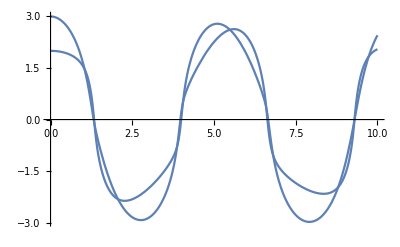

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

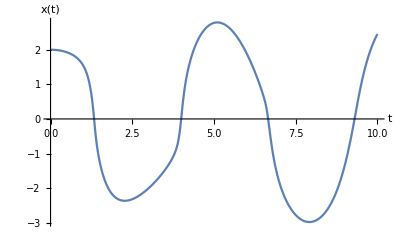

```mathematica
Plot[ q[[1]] /. solution , { t, 0, 10 }, AxesLabel-> { t, q[[1]] } ]
```

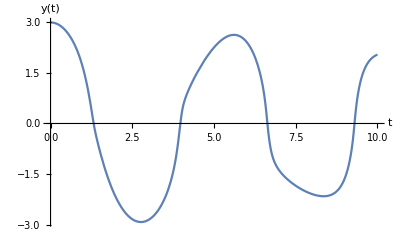

```mathematica
Plot[ q[[2]] /. solution , { t, 0, 10 } , AxesLabel-> { t, q[[2]] }]
```

```mathematica
D[V, x[t]]
```

g m (2 x[t]-y[t])

```mathematica
D[V, y[t]]
```

g m (-x[t]+2 y[t])

```mathematica
Solve[Union[ D[V, x[t]] == 0 , D[V, y[t]]== 0  ] , q ]
```

{{x[t]→0,y[t]→0}}

```mathematica
(* 
*)
```